```mathematica
area1raw = RandomVariate[BinomialDistribution[100, 0.5], 1000];
```

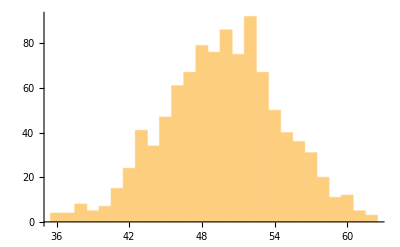

```mathematica
Histogram[area1raw]
```

```mathematica
area1prop = RandomVariate[BinomialDistribution[100, 0.5], 10000]/100;
```

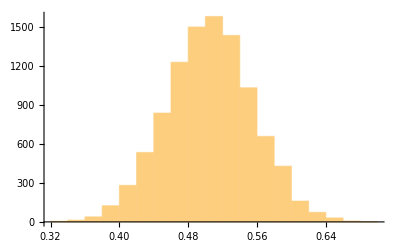

```mathematica
Histogram[area1prop]
```

```mathematica
area2prop = RandomVariate[BinomialDistribution[100, 0.5], 10000]/100;
```

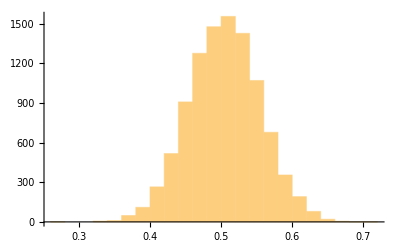

```mathematica
Histogram[area2prop]
```

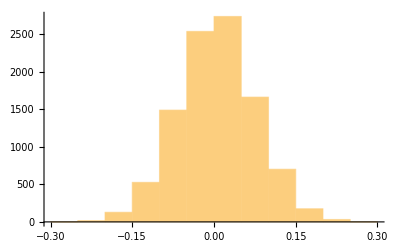

```mathematica
Histogram[area1prop - area2prop]
```